1. Calcule as integrais múltiplas iteradas:

a) ∫_0^3 ∫_-2^0 x^2 y-2x yⅆyⅆx.

∫_-2^0 x^2 y-2x yⅆy=∫_-2^0 x^2 yⅆy-2∫_-2^0 x yⅆy=
x^2 y^2/2(|_(y=-2))^(y=0)-2 x y^2/2(|_(y=-2))^(y=0)=
x^2(0-2)-2x(0-2)=
-2 x^2+4x.

∫_0^3 -2 x^2+4xⅆx=
-2(∫_0)^3 x^2 ⅆx+4∫_0^3 xⅆx=
-2 x^3/3|_(x=0)^(x=3)+4 x^2/2(|_(x=0))^(x=3)=
-2(9-0)+4(9/2-0)=
-18+18=0.

```mathematica
Integrate[x^2 y-2x y,{x,0,3},{y,-2,0}]
```

0

b) ∫∫_T ∫x+2y+3zⅆv, onde
T={0≤x≤2
0≤y≤3
1≤z≤3 .

Qualquer ordem de integração; então x, y, z.

∫_1^3 ∫_0^3 ∫_0^2 x+2y+3zⅆv=
∫_1^3 ∫_0^3 ∫_0^2 x+2y+3zⅆxⅆyⅆz=
∫_1^3 ∫_0^3 x^2/2+2x y+3x z|_(x=0)^(x=2) ⅆyⅆz=
∫_1^3 ∫_0^3 2+4 y+6 zⅆyⅆz=
∫_1^3 2y+2 y^2+6y z|_(y=0)^(y=3)ⅆz=
∫_1^3 6+18+18zⅆz=
6z+18z+9 z^2|_1^3=
18+54+81-(6+18+9)=
153-33=120.

```mathematica
{Integrate[x+2y+3z,{x,0,2},{y,0,3},{z,1,3}],Integrate[x+2y+3z,x],18+27+81-(6+9+9),Integrate[x+2y+3z,x],Integrate[2+4y+6z,y],Integrate[24+18z,z],18+54+81-(6+18+9)}
```

{120,x^2/2+2 x y+3 x z,102,x^2/2+2 x y+3 x z,2 y+2 y^2+6 y z,24 z+9 z^2,120}

2. Dada a integral I=∫_0^1 ∫_(x^2)^x ⅆyⅆx:

a) Descreva analiticamente a região de integração.

A região de integração é a região delimitada no eixo y pelas funções y=x e y=x^2 e no eixo x pelo intervalo 0≤x≤1. Ou x^2≤y≤x∧0≤x≤1.

b) Descreva graficamente a região de integração.

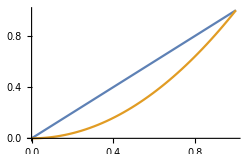
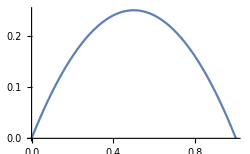
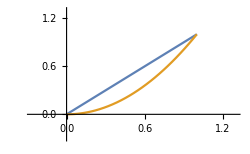
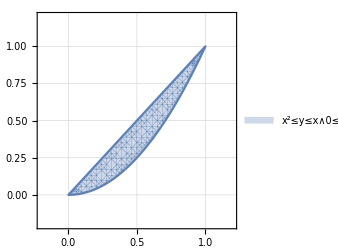

```mathematica
Row[{Plot[{x,x^2},{x,0,1},ImageSize->250],Plot[x-x^2,{x,0,1},ImageSize->250],Plot[{x,x^2},{x,-0.3,1.3},PlotRange->{-0.3,1.3},RegionFunction->Function[{x},0≤x≤1],ImageSize->250],RegionPlot[x^2≤y≤x&&0≤x≤1,{x,-0.2,1.2},{y,-0.2,1.2},ImageSize->250,PlotTheme->"Detailed"]},Spacer[10]]
```

c) Calcule a integral utilizando uma “ordem” escolhida.

∫_0^1 ∫_(x^2)^x ⅆyⅆx=
∫_0^1 y|_(y=x^2)^(y=x)ⅆx=
∫_0^1 x-x^2 ⅆx=
x^2/2-x^3/3|_0^1=
(3 x^2-2 x^3)/6|_0^1=
(3-2)/6=1/6.

```mathematica
{Integrate[1,{y,x^2,x},{x,0,1}],Integrate[x-x^2,{x,0,1}]}
```

{x-x^2,1/6}

3. Determine a área da região limitada pelas curvas y=x+1 e y=3+2x-x^2 (usando obrigatoriamente uma integral dupla). Represente a região graficamente.

f(x)=x+1, 
g(x)=3+2x-x^2.

x+1=3+2x-x^2⇒
-x^2+x+2=0⇒
x=(-1±√(1-4·-1·2))/-2=
x=(-1±3)/-2={-1
2.

f(1)=2 e g(1)=4.
g(x)>f(x).

∫_-1^2 g(x)-f(x)ⅆx=∫_-1^2 -x^2+2x+3-x-1ⅆx=∫_-1^2 -x^2+x+2ⅆx=
-x^3/3+x^2/2+2x|_-1^2=-8/3+2+4-(1/3+1/2-2)=
(-8+6+12)/3-((2+3-12)/6)=10/3+7/6=27/6.

```mathematica
{Solve[-x^2+x+2==0,x],#+1&@@1,3+(2#)-(#^2)&@@1,Function[x,3+2x-x^2][1],3+2x-x^2-(x+1),Integrate[-x^2+x+2,x],Integrate[-x^2+x+2,{x,-1,2}]}
```

{{{x→-1},{x→2}},1,1,4,2+x-x^2,2 x+x^2/2-x^3/3,9/2}

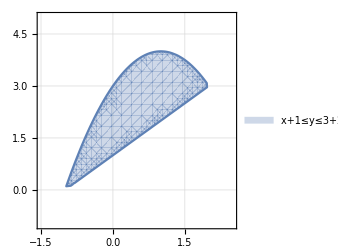

```mathematica
RegionPlot[x+1≤y≤3+2x-x^2&&-1≤x≤2,{x,-1.5,2.5},{y,-1,5},ImageSize->250,PlotTheme->"Detailed"]
```

Professor: “(a integral dupla) pode ser usada para calcular área: ∫∫1ⅆxⅆy...” ∫∫ⅆxⅆy=∫xⅆy=x y.
“A região de integração fica...” Ficaria (∫∫)_R ⅆxⅆy, em que R=x+y<y<3+2x-x^2.

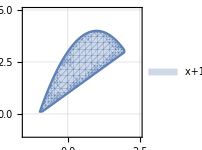

```mathematica
RegionPlot[x+1≤y≤3+2x-x^2,{x,-1.5,2.5},{y,-1,5},ImageSize->150,PlotTheme->"Detailed"]
```

Eu passei os pontos de intersecção na região acima, mas sem passar a região é exatamente a mesma, pois é “a única” área entre as duas funções. Se a região tivesse mais áreas entre as funções, eu estaria limitando artificialmente, portanto deveria considerar em toda sua extensão... ou a equalização das funções já expressa todos os pontos de intersecção, e por isso há confiança que são apenas estes.

Convertendo esta região em integrais iteradas...

∫_(x+1)^(3+2x-x^2) (∫^2)_-1 ⅆxⅆy=
∫_(x+1)^(3+2x-x^2) 3ⅆy=
3∫_(x+1)^(3+2x-x^2) ⅆy=
3·y(|_(x+1))^(3+2x-x^2)=
3·[3+2x-x^2-(x+1)]=
3·(2+x-x^2)=6+3x-3x^2. Não.

Eu acho que é o contrário.

(∫^2)_-1∫_(x+1)^(3+2x-x^2) ⅆxⅆy=
(∫_-1)^2 x(|_(x+1))^(3+2x-x^2)ⅆy=
(∫_-1)^2 3+2x-x^2-(x+1)ⅆy=
(∫^2)_-1 2+x-x^2 ⅆy=
2x y+x^2/2 y-x^3/3 y(|^(y=2))_(y=-1)=
4x+x^2-2/3 x^3-(-2x-x^2/2+x^3/3)=
4x+x^2-2/3 x^3+2x+x^2/3-x^3/3=
6x+4/3 x^2-x^3. Não.

ou

(∫^2)_-1∫_(x+1)^(3+2x-x^2) ⅆyⅆx=
(∫_-1)^2 y|_(x+1)^(3+2x-x^2)ⅆx=
(∫^2)_-1 y(3+2x-x^2)-y(x+1)ⅆx=
(∫^2)_-1 3y+2y x-y x^2-y x-yⅆx=
(∫^2)_-1 2y+y x-y x^2 ⅆx=
2y x+y x^2/2-y x^3/3(|^(x=2))_(x=-1)=
4y+2y-8/3 y-(-2y+y/2+y/3)=
10/3 y+7/6 y=27/6 y.

```mathematica
{Integrate[1,{y,x+1,3+2x-x^2}],
Integrate[1,{y,x,2x}],Expand@Integrate[1,{y,x+1,3+2x-x^2},{x,-1,2}],Expand@Integrate[1,{x,x+1,3+2x-x^2},{y,-1,2}],
Expand@Integrate[1,{x,-1,2},{y,x+1,3+2x-x^2}](*esse*),
Expand@Integrate[1,{y,-1,2},{x,x+1,3+2x-x^2}]}
```

{2+x-x^2,x,6+3 x-3 x^2,6+3 x-3 x^2,9/2,6+3 x-3 x^2}

Por algum motivo, y(|^(2x))_x=2x-x=x, e não y(2x-x)=y x.
Compreender este operador melhor, ele é uma espécie de aplicação e não substituição.

(∫^2)_-1∫_(x+1)^(3+2x-x^2) ⅆyⅆx=
(∫_-1)^2 y|_(x+1)^(3+2x-x^2)ⅆx=
(∫^2)_-1 3+2x-x^2-(x+1)ⅆx=
(∫^2)_-1 2+ x- x^2 ⅆx=
2x+ x^2/2-x^3/3(|^2)_-1=
4+2-8/3-(-2+1/2+1/3)=
10/3+7/6=27/6.

4. Determine o volume do prisma cuja base é o triângulo no plano x y limitado pelo eixo x e pelas retas y=x e x=2 e cujo topo está no plano z=f(x,y)=4-x-y.

(∫∫)_R 4-x-yⅆV, R={y=x
x=2.

A primeira integral ∫4-x-yⅆx. Em respeito a x... é preciso encontrar as intersecções. No caso, no eixo x com o eixo y e o eixo z. y e x se encontram em (2,2). Neste ponto, z=0. O outro limite de x está no enunciado, em x=0. Então (∫_0)^2 4-x-yⅆx.

A segunda integral ∫4-x-yⅆy. Em respeito a y, em x=0, y=0, e em x=2, y=2. Então (∫^2)_0 4-x-yⅆy.

(Obviamente, z já é o limite em função de x e y.)

Em x=0, y=0 e em x=2, y=2.

(∫^2)_0(∫^2)_0 4-x-yⅆxⅆy=
(∫^2)_0 4x-x^2/2-y x(|_(x=0))^(x=2)ⅆy=
(∫^2)_0 8-2-2yⅆy=
6y-y^2(|^2)_0=8.

(∫^x)_0(∫^2)_0 4-x-yⅆxⅆy=
(∫^x)_0 4x-x^2/2-y x(|_(x=0))^(x=2)ⅆy=
(∫^x)_0 8-2-2yⅆy=
6y-y^2(|^(y=x))_(y=0)=
3 x^2-x^3/3.

Na outra ordem de integração.

(∫^2)_0(∫^x)_0 4-x-yⅆyⅆx=
(∫^2)_0 4y-x y-y^2/2(|_(y=0))^(y=x)ⅆx=
∫_0^2 4x-x^2-x^2/2 ⅆx=
2 x^2-x^3/3-x^3/6|_0^2=
8-8/3-4/3=4.

```mathematica
{Integrate[y,x],Integrate[4-x-y,{x,0,2},{y,0,2}],Integrate[6y-y^2,{y,0,x}],Integrate[4-x-y,{y,0,x}],Integrate[4-x-y,y],Integrate[4-x-y,{y,0,x},{x,0,2}],Integrate[4x-x^2-x^2/2,x],Integrate[4x-x^2-x^2/2,{x,0,2}],Integrate[x^2/2,x]}
```

{x y,8,3 x^2-x^3/3,(4-x) x-x^2/2,4 y-x y-y^2/2,6 x-x^2,2 x^2-x^3/2,4,x^3/6}

5. Calcule a integral (∫∫)_R ⅇ^(x^2+y^2)ⅆyⅆx, onde R é a região semicircular limitada pelo eixo x e pela curva y=√(1-x^2).

Em x=0, y=1.

√(1-x^2)=x⇒1-x^2=x^2⇒2 x^2=1⇒x=√(1/2)=1^(1/2)/2^(1/2)=1/(√2).

Em x=1/(√2), y=√(1-(1/(√2))^2)=√(1-1/2)=√(1/2)=1/(√2).

Errado. √(1-x^2)=x significa encontrar a intersecção com a linha y=x, que ocorre em 1/(√2) que é um ponto entre 0 e 1:

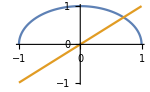

```mathematica
Plot[{√(1-x^2),x},{x,-1,1},ImageSize->150]
```

Encontrar a intersecção com o eixo x significa y=0 e √(1-x^2)=0⇒x^2=1⇒x=(-1,1).

(∫^(1/(√2)))_0(∫^(1/(√2)))_1 ⅇ^(x^2+y^2)ⅆyⅆx=
(∫^(1/(√2)))_0(∫^(1/(√2)))_1 ⅇ^(x^2+y^2)ⅆyⅆx=

```mathematica
{√(1/2),N@(1/(√2)),Integrate[ⅇ^x,x],Integrate[ⅇ^(a x),x],Integrate[ⅇ^(x^2),x],Integrate[ⅇ^(x^2+y^2),y],Integrate[ⅇ^x,x],Integrate[ⅇ^(x^2),x],Red@Integrate[ⅇ^(x^2+y^2),{y,1,1/(√2)},{x,0,1/(√2)}],Blue@(1/a^(-(x+y))),Integrate[ⅇ^(-(x^2+y^2)),x],Integrate[ⅇ^(-x^2),x],Integrate[ⅇ^(-(x^2+y^2)),{x,-∞,∞},{y,-∞,∞}],Integrate[ⅇ^(-x^2),{x,-∞,∞}],Integrate[ⅇ^(-x^2),{x,0,1/(√2)}],N@π,N@1/√2}
```

{1/(√2),0.707107,ⅇ^x,ⅇ^(a x)/a,1/2 √π Erfi[x],1/2 ⅇ^(x^2) √π Erfi[y],ⅇ^x,1/2 √π Erfi[x],(RGBColor[1, 0, 0])[1/4 π Erfi[1/(√2)] (-Erfi[1]+Erfi[1/(√2)])],(RGBColor[0, 0, 1])[a^(x+y)],1/2 ⅇ^(-y^2) √π Erf[x],1/2 √π Erf[x],π,√π,1/2 √π Erf[1/(√2)],3.14159,0.707107}

Wolfram1: The error function Erf[z] is the integral of the Gaussian distribution, given by erf(z)=2/(√π)(∫^z)_0 ⅇ^(-t^2)ⅆt. The imaginary error function Erfi[z] is given by erfi(z)=(erf(i z))/i. The generalized error function Erf[z0,z1] is defined by the integral 2/(√π)(∫^z_1)_z_0 ⅇ^(-t^2)ⅆt. The error function is central to many calculations in statistics.

Wikipedia2: 
((∫^∞)_(-∞)ⅇ^(-x^2)ⅆx)^2=
(∫^∞)_(-∞)ⅇ^(-x^2)ⅆx (∫^∞)_(-∞)ⅇ^(-y^2)ⅆy=
(∫^∞)_(-∞)(∫^∞)_(-∞)ⅇ^(-x^2)ⅇ^(-y^2)ⅆxⅆy=
(∫^∞)_(-∞)(∫^∞)_(-∞)ⅇ^(-x^2-y^2)ⅆxⅆy.

(Porquê ⅆxⅆy e não ⅆyⅆx?)

Caminho reverso:

∫∫ⅇ^(-(x^2+y^2))ⅆxⅆy=
∫∫ⅇ^(-x^2)ⅇ^(-y^2)ⅆxⅆy=
∫ⅇ^(-x^2)ⅆx∫ⅇ^(-y^2)ⅆy=
(∫ⅇ^(-x^2)ⅆx)^2.

No caso do exercício,

(∫^(1/(√2)))_0(∫^(1/(√2)))_1 ⅇ^(x^2+y^2)ⅆyⅆx=
(∫^(1/(√2)))_0(∫^(1/(√2)))_1 1/(ⅇ^(-(x^2+y^2)))ⅆyⅆx=
(∫^(1/(√2)))_0(∫^(1/(√2)))_1 ⅇ^(x^2)ⅇ^(y^2)ⅆyⅆx=
(∫^(1/(√2)))_0(∫^(1/(√2)))_1 1/(ⅇ^(-x^2))1/(ⅇ^(-y^2))ⅆyⅆx=nada.

Só que

∫ⅇ^x ⅆx=ⅇ^x+C⇒
(∫ⅇ^(-x^2)ⅆx)^2=(ⅇ^(-x^2))^2+C=ⅇ^(-x^4)+C? Não.

E por isso é necessária a integração polar.

O eixo x significa θ=0.

A curva y=√(1-x^2) significa...

√(1-x^2)=
√(1-(r cosθ)^2)=
√(1-r^2 cos^2 θ)=
√1...

Se soubermos que r=1,

√(1-x^2)=
√(1-(r cosθ)^2)=
√(1-cos^2 θ)=
sinθ. ?

“Esta questão deve ser resolvida por coordenadas polares: 0≤θ≤π e 0≤r≤1 e (∫∫)_R ⅇ^(r^2)ⅆrⅆθ. A representação gráfica (software) fica y=√(1-x^2) que dá um semi circulo na parte positiva. Vai fechar o resultado.”

y=√(1-x^2) corresponde ao semicírculo x^2+y^2=a porque a=1 e y^2=1-x^2⇒y=√(1-x^2).

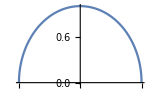

```mathematica
Plot[√(1-x^2),{x,-1,1},ImageSize->150]
```

Chegamos às coordenadas da curva visualmente.

0≤r≤1, 
0≤θ≤π.

(∫∫)_R ⅇ^(x^2+y^2)ⅆyⅆx=
(∫_0)^π(∫_0)^1 ⅇ^(r^2)rⅆrⅆθ=
(u=r^2,ⅆu=2rⅆr)
(∫^π)_0(∫^1)_0 ⅇ^u/2 ⅆuⅆθ=
(∫^π)_0(ⅇ^(r^2))/2(|^(r=1))_(r=0)ⅆθ=
(∫^π)_0 ⅇ/2-1/2 ⅆθ=
ⅇθ/2-θ/2(|^(θ=π))_(θ=0)=
(ℼ ⅇ-π)/2.

Está (estava) errado pois ∫ⅇ^(r^2)≠ⅇ^(r^2). Substituição?

```mathematica
{Integrate[ⅇ-1,θ],Integrate[ⅇ^(r^2),r],Integrate[ⅇ^(r^2),{r,0,1}],N@ⅇ π-π,Integrate[ⅇ^(r^2)r,r],Expand@Integrate[ⅇ^(r^2)r,{r,0,1},{θ,0,π}]}
```

{-θ+ⅇ θ,1/2 √π Erfi[r],1/2 √π Erfi[1],5.39814,(ⅇ^(r^2))/2,-π/2+(ⅇ π)/2}

“Na integral por coordenadas polares está faltando um r, assim a integral deve ser ∫∫er^2.r.drdθ, sendo que os limites de integração são 0≤r≤1 e 0≤θ≤π (a função y=√(1-x2) que é uma semicircular), então usa o processo da integração por substituição fazendo u=r^2 em que du= 2rⅆr.”

6. Calcule o comprimento da cardioide r=3+3cosθ.

θ_0=0, θ_1=π.
f'(θ)=(ⅆ3+3cosθ)/ⅆθ=-3senθ.
s=2∫_0^π √((-3senθ)^2+(3+3cosθ)^2)ⅆθ=
2∫_0^π √(9 sen^2 θ+9+18cosθ+9 cos^2 θ)ⅆθ=
2∫_0^π √(9(sen^2 θ+cos^2 θ)+9+18cosθ)ⅆθ=
2∫_0^π √(18+18cosθ)ⅆθ=
2∫_0^π √(18(1+cosθ))ⅆθ=
2∫_0^π √18 √(1+cosθ)ⅆθ=
√36∫_0^π √(1+cosθ)ⅆθ=
√36∫_0^π √(2 cos^2 θ/2)ⅆθ=
2 √36∫_0^π √(cos^2 θ/2)ⅆθ=
2 √36∫_0^π cos θ/2 ⅆθ.

u=θ/2, ⅆu=1/2 ⅆx.

∫cos θ/2 ⅆθ=∫cos(u)·2ⅆu=2∫cos uⅆu=2sen u=2senθ/2.

2 √36∫_0^π cos θ/2 ⅆθ=
2 √36(2 sen θ/2)(|^π)_0=24.

No livro (p. 145):

sen^2 θ+1+2cosθ+cos^2 θ=
1+1+2cosθ.

A regra é a “identidade Pitagoreana” de que sen^2 θ+cos^2 θ=1.

E:

(∫^π)_0 √(2+2cosθ)ⅆθ=
√2(∫_0)^π √(1+cosθ)ⅆθ.

É porque

(∫^π)_0 √(2+2cosθ)ⅆθ=
(∫^π)_0 √(2(1+cosθ))ⅆθ=
(∫^π)_0 √2 √(1+cosθ)ⅆθ=
√2(∫_0)^π √(1+cosθ)ⅆθ.

√(a b)=(a b)^(1/2)=a^(1/2)b^(1/2)=√a √b. Está no Algebra.

Finalmente, a relação cos θ/2=±√((1+cosθ)/2)?

Dá para fatorar a relação.

(cos θ/2)^2=(±√((1+cosθ)/2))^2⇒
cos^2 θ/2=(1+cosθ)/2⇒
2 cos^2 θ/2=1+cosθ.

Que é a relação aludida (novamente sem qualquer comentário) na p. 145.
É uma “half-angle formula”.

Final... 2·2sen θ/2(|^π)_0=4. É porque sen π/2=1.

Mas antes,
∫cos θ/2 ⅆθ≠sen θ/2;
∫cos θ/2 ⅆθ=2sen θ/2. Porque?

Porque é uma substituição. Como na AD1, em sen x/3, procurar uma função que multiplique sua derivada. Resolvido na questão.

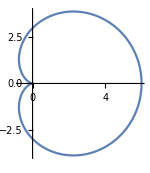

```mathematica
PolarPlot[3+3Cos[θ],{θ,0,2π},ImageSize->150]
```

```mathematica
{D[Cos[θ],θ],D[3Cos[θ],θ],D[3+3Cos[θ],θ],(-√a)^2,Sin[0],Sin[π],Sin[π/2],Integrate[√((-3Sin[θ])^2+(3+3Cos[θ])^2),{θ,0,π}],Expand[(-3Sen[θ])^2+(3+3Cos[θ])^2],Integrate[√(18(1+Cos[θ])),{θ,0,π}],Integrate[Cos[θ/2],θ]}
```

{-Sin[θ],-3 Sin[θ],-3 Sin[θ],a,0,0,1,12,9+18 Cos[θ]+9 Cos[θ]^2+9 Sen[θ]^2,12,2 Sin[θ/2]}

7. Determine o volume do sólido gerado pela rotação em torno do eixo x da região limitada  por y=x^2+1 e a reta y=x+3.

x^2+1=x+3⇒
x^2-x-2=0⇒
x=(1±√(1+8))/2={2
-1.

V=∫_-1^2 (π(x+3))^2-(π(x^2+1))^2 ⅆx=
∫_-1^2 π(x^2+6x+9)-π(x^4+2 x^2+1)ⅆx=
(∫^2)_-1 π(x^2+6x+9-x^4-2 x^2-1)ⅆx=
π(∫^2)_-1-x^4-x^2+6x+8ⅆx=
π(-x^5/5-x^3/3+3 x^2+8x)(|^2)_-1=

π(-32/5-8/3+12+16)-π(1/5+1/3+3-8)=
π((-96-40+180+240)/15)-π((3+5+45-120)/15)=
π(284/15)-π(-67/15)=(351π)/15.

```mathematica
{Expand[π(x+3)^2-π(x^2+1)^2],-96-40+180+240,Integrate[π(x+3)^2-π(x^2+1)^2,{x,-1,2}],351/3}
```

{8 π+6 π x-π x^2-π x^4,284,(117 π)/5,117}

8. Fórum 2. Pesquisar e apresentar situação problema com a resolução usando software matemático. Escreva um comentário de ao menos 8 linhas sobre a importância da utilização desse software nesta solução.

gkwcj_shm78FrontEndObject[LinkObject["gkwcj_shm", 3, 1]]78Untitled-6

Uma torta de maçã precisa de 1 kg de maçãs  para ser confeccionada. Quantas maçãs são necessárias adquirir, sendo que:

A maçã é um sólido de revolução de uma curva cardióide descrita por r=2-2senθ, com r em cm;

O centro da maçã deve ser desprezado e é descrito por um cilindro de largura 1.2cm.

A densidade da maçã é de 20 g/cm^3.

Converteremos a cardióide de coordenadas polares para retangulares:

r=1-senθ⇒
r^2=r-r senθ⇒
r^2=r-y⇒
y=-r^2-r⇒
y=-(√(x^2+y^2))^2-√(x^2+y^2)⇒
y=-(x^2+y^2)-√(x^2+y^2). Não.

r=1-senθ⇒
r^2=r-r senθ⇒
r^2=r-y⇒
x^2+y^2=r-y⇒
r=x^2+y^2+y⇒
r^2=(x^2+y^2+y)^2⇒
x^2+y^2=(x^2+y^2+y)^2⇒

x^2+y^2=x^4+2 x^2 y+y^2+2 x^2 y^2+2 y^3+y^4⇒
y^2=x^4+2 x^2 y+y^2+2 x^2 y^2+2 y^3+y^4-x^2... Não.

```mathematica
{Expand@((x^2+y^2)^2),Expand@((x^2+y^2+y)^2),FullSimplify@(x^4)+2 x^2 y+y^2+2 x^2 y^2+2 y^3+y^4-x^2}
```

{x^4+2 x^2 y^2+y^4,x^4+2 x^2 y+y^2+2 x^2 y^2+2 y^3+y^4,-x^2+x^4+2 x^2 y+y^2+2 x^2 y^2+2 y^3+y^4}

y=-a-√a⇒
y=-(a+√a)⇒
y=-(a^1+a^(1/2))⇒
y^2=-(a^1+a^(1/2))^2⇒
y^2=-(a^2+2a a^(1/2)+a^(1/2 2))⇒
y^2=-(a^2+2 a^(3/2)+a)⇒
y^2=-a(a+2 a^(1/2)+1). Não.

r=1-senθ⇒
r=1-y/r⇒
r^2=r-y⇒
y=-r^2+r⇒
y=-(√(x^2+y^2))^2+√(x^2+y^2)⇒
y=-(x^2+y^2)+√(x^2+y^2).

Está correta. Curva implícita.

Ou com tamanho dobrado...

r=2-2senθ⇒
r=2-2 y/r⇒
r=(2r-2y)/r⇒
r^2=2r-2y⇒
y=(-r^2+2r)/2⇒
y=(-(√(x^2+y^2))^2+2 √(x^2+y^2))/2⇒
y=(-(x^2+y^2)+2 √(x^2+y^2))/2.

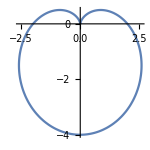
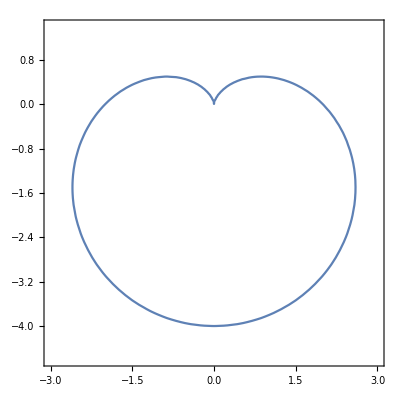
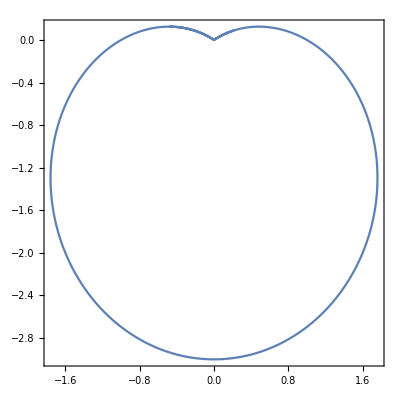

```mathematica
{PolarPlot[2-2Sin[θ],{θ,0,2π},ImageSize->150],ContourPlot[(-(x^2+y^2)+2 √(x^2+y^2))/2==y,{x,-3,3},{y,-4.6,1.4}],RegionPlot[ImplicitRegion[(-(x^2+y^2)+√(x^2+y^2))/2==y,{x,y}]]}
```

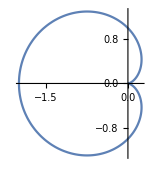
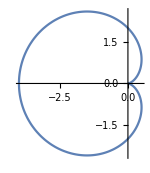
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{RevolutionPlot3D[1-Sin[t],{t,1,10}],PolarPlot[1-Cos[θ],{θ,0,2π},ImageSize->150],PolarPlot[2-2Cos[θ],{θ,0,2π},ImageSize->150]}
```

```mathematica
{Integrate[π(2-2Sin[θ])^2,{θ,-3,3}],N@Integrate[π(2-2Sin[θ])^2,{θ,-3,3}],N@Integrate[π(2-2Sin[θ])^2,{θ,-4,4}],N@Integrate[2-2Sin[θ],{θ,0,2π}],Red@Integrate[π(2-2Sin[θ])^2,{θ,0,2π}],
Integrate[π(2-2Cos[θ])^2,{θ,0,2π}]}
```

{-2 π (-18+Sin[6]),114.853,144.58,12.5664,(RGBColor[1, 0, 0])[12 π^2],12 π^2}

Encontrar onde a função “cruza” os limites de integração? Mas e se a função for mais “gordinha” para cima ou para baixo (e a maçã é)? Não seria encontrar o máximo no eixo?

Talvez não porque não é “largura”.
Principalmente ao integrar em polar, em que os limites, se a integração é em termos do ângulo, são em radianos.

Mas igualar y=0 é para coordenadas cartesianas. Em polares, o intervalo de integração é em quadrantes.

Talvez as fórmulas de revolução não valham para polar. Por isso, a transformação em cartesiano já feita. O problema é que aí o intervalo de integração passa a exigir máximo.

Segundo o Wolfram, a área de uma cardióide é (3π a^2)/2 para r(θ)=a(1-cosθ).

Mas não conseguirei integrar a cardióide cartesiana pois a conversão de polar resultou em uma função implícita, em duas variáveis.

3: é integrada com uma integral dupla em r e depois em θ.

A=(∫_0)^θ(∫_0)^r r ⅆrⅆθ=
(∫_0)^(2π)(∫_0)^(2-2senθ)rⅆrⅆθ=
(∫_0)^(2π)r^2/2(|_(r=0))^(r=2-2senθ)ⅆθ=
(∫^(2π))_0(2-2senθ)^2/2 ⅆθ=
(∫^(2π))_0(4-2·2·(2senθ)+4 sen^2 θ)/2 ⅆθ=
(∫^(2π))_0 2-4senθ+2 sen^2 θⅆθ=
2θ+4cosθ+2(θ/2-(sen 2θ)/4)(|^(θ=2π))_(θ=0)=
2θ+4cosθ+θ-(sen 2θ)/2(|^(θ=2π))_(θ=0)=
4π+4+2π-4=6π.

```mathematica
{Integrate[r,{r,0,2-2Sin[θ]},{θ,0,2π}],Integrate[(2-2Sin[θ])^2/2,{θ,0,2π}]}
```

{π (2-2 Sin[θ])^2,6 π}

Porquê o primeiro não substitui r=2-2senθ?

```mathematica
{Expand@((2-2Sin[θ])^2),Expand@((2-2Sin[θ])^2/2),Integrate[2-4Sin[θ]+2 Sin[θ]^2,θ],Integrate[Sin[θ]^2,θ],Sin[0]}
```

{4-8 Sin[θ]+4 Sin[θ]^2,2-4 Sin[θ]+2 Sin[θ]^2,3 θ+4 Cos[θ]-1/2 Sin[2 θ],θ/2-1/4 Sin[2 θ],0}

Não sei como obter o volume de rotação a partir da área.

4:

V=(∫^θ_2)_θ_1 6πⅆθ=
6π θ(|^(2π))_0=
12π^2.

A fórmula do método disco (∫^θ_2)_θ_1 π[f(r)]^2 ⅆθ para volume de revolução da polar estava correta.

O cilindro.

V=(∫^θ_2)_θ_1 2π r f(r)ⅆr=
(∫^θ_2)_θ_1 2π r(2-2senθ)ⅆr=
(∫^θ_2)_θ_1 4π r-4π r senθⅆr=
2π r^2+2π r^2 cos θ(|^(2π))_0=
8 π^3+8 π^3 cosθ ... Não.

Pegando apenas metade da área de integração pega apenas o topo?
Mas preciso do topo limitado pelo intervalo.

Não vai dar tempo para fazer o miolo.

1	tutorial/SpecialFunctions

2	https://en.wikipedia.org/wiki/Gaussian_integral

3	https://socratic.org/questions/how-do-i-find-the-area-inside-a-cardioid

4	http://tutorial.math.lamar.edu/Classes/CalcI/Area_Volume_Formulas.aspx